```mathematica
Clear["Global`*"]
```

# Unbalanced Lattice

## Constants

```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .529177*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;

el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
kK=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;

λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 282*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency clock trans ??? *)
```

```mathematica
λl =λ813 √2;
kl = (2Pi)/λl;
Er = (ℏ kl)^2/(2m);
U=5Er;
J = 4/(√π)Er(U/Er)^(3/4)Exp[-2 √(U/Er)];
```

```mathematica
J/(2π ℏ)
```

149.434

Coupled phases:

```mathematica
k = 2 π/λ813;
Ef[x_,ϕ_]:= Exp[I (k x+ϕ)];
Uj[x_,y_,T_,ϕ0_,ϕ1_]:=Abs[T^(1/2)Ef[x,0]+T^(7/2) Ef[-x,2ϕ0+ϕ1]+T^(3/2) Ef[y,ϕ0]+T^(5/2) Ef[-y,ϕ0+ϕ1]]^2*U/(16J);
Manipulate[DensityPlot[Uj[x,y, T, ϕ0,ϕ1],{x,0,2λ813},{y,0,2λ813},PlotPoints->50],{{T, 1, "Transmission"},0,1},{{ϕ0, 0, "ϕ0"},0,2π},{{ϕ1, 0, "ϕ1"},0,2π}]
```

```mathematica
Manipulate[Plot[{Uj[x,x,T,0,0],Uj[x,-x,T,0,0]},{x,0,λ813 √2}],{{T,1,"Transmission"},0,1}]
```

Plot::plln: Limiting value √2 λ813 in {x,0,√2 λ813} is not a machine-sized real number.

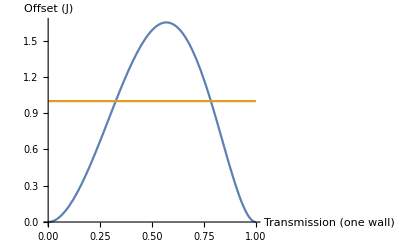

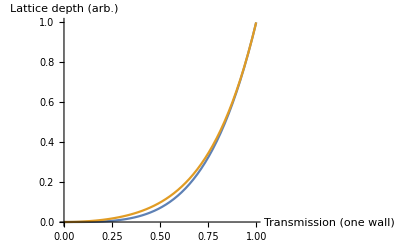

```mathematica
x=λ813/4;
Plot[{Uj[x,x,T,0,0]-Uj[x,-x,T,0,0],1},{T,0,1},AxesLabel->{"Transmission (one wall)","Offset (J)"}]
Plot[{(Uj[0,0,T,0,0]-Uj[x,x,T,0,0])J/U,(Uj[0,0,T,0,0]-Uj[x,-x,T,0,0])J/U},{T,0,1},AxesLabel->{"Transmission (one wall)","Lattice depth\n(arb.)"}]
```

```mathematica
Uy=(Uj[0,0,T,0,0]-Uj[x,x,T,0,0])J/U;
Ux = (Uj[0,0,T,0,0]-Uj[x,-x,T,0,0])J/U;
U0 = 5 Er;
U1=Uy/Ux U0;
J0 = 4/(√π)Er(u/Er)^(3/4)Exp[-2 √(u/Er)]/.u-> U0;
J1 = 4/(√π)Er(u/Er)^(3/4)Exp[-2 √(u/Er)]/.u-> U1;
```

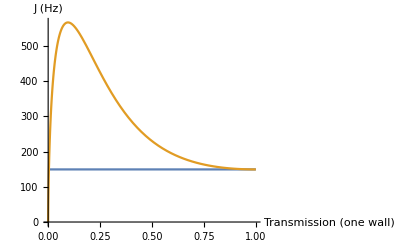

```mathematica
Plot[{J0/(2π ℏ),J1/(2π ℏ)},{T,0,1},AxesLabel->{"Transmission (one wall)","J (Hz)"}]
```

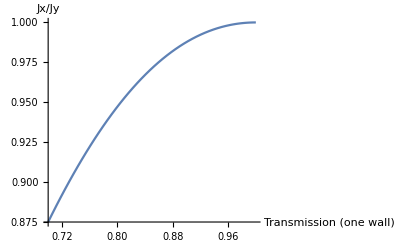

```mathematica
Plot[{(J0/(2π ℏ))/(J1/(2π ℏ))},{T,0.7,1},AxesLabel->{"Transmission (one wall)","Jx/Jy"}]
```